# MFEM Mesh Generation

MFEM Geometry types:
# POINT       		= 0
# SEGMENT     		= 1
# TRIANGLE    		= 2
# SQUARE      		= 3
# TETRAHEDRON 	= 4
# CUBE        		= 5

Units are in meters m

```mathematica
<<NDSolve`FEM`
<<MeshTools`
```

## Figures

```mathematica
PDMScylinder = Cylinder[{{0,0,0},{0,0,3}},5];
Graphics3D[{FaceForm[LightBlue], PDMScylinder,
Black,Arrowheads[0.03],Arrow[Tube[{{0,0,4.5},{0,0,3}},0.02]],
Black,Arrowheads[0.03],Arrow[Tube[{{1,0,4.5},{1,0,3}},0.02]],
Black,Arrowheads[0.03],Arrow[Tube[{{2,0,4.5},{2,0,3}},0.02]],
Black,Arrowheads[0.03],Arrow[Tube[{{3,0,4.5},{3,0,3}},0.02]],
Black,Arrowheads[0.03],Arrow[Tube[{{-1,0,4.5},{-1,0,3}},0.02]],
Black,Arrowheads[0.03],Arrow[Tube[{{-2,0,4.5},{-2,0,3}},0.02]],
Black,Arrowheads[0.03],Arrow[Tube[{{-3,0,4.5},{-3,0,3}},0.02]]
},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
PDMScylinder = Cylinder[{{0,0,0},{0,0,3}},5];
Graphics3D[{FaceForm[LightBlue], PDMScylinder,
Black,Arrowheads[0.03],Arrow[Tube[{{0,0,4.5},{0.4,0,3}},0.02]],
Black,Arrowheads[0.03],Arrow[Tube[{{1,0,4.5},{1.4,0,3}},0.02]],
Black,Arrowheads[0.03],Arrow[Tube[{{2,0,4.5},{2.4,0,3}},0.02]],
Black,Arrowheads[0.03],Arrow[Tube[{{3,0,4.5},{3.4,0,3}},0.02]],
Black,Arrowheads[0.03],Arrow[Tube[{{-1,0,4.5},{-0.6,0,3}},0.02]],
Black,Arrowheads[0.03],Arrow[Tube[{{-2,0,4.5},{-1.6,0,3}},0.02]],
Black,Arrowheads[0.03],Arrow[Tube[{{-3,0,4.5},{-2.6,0,3}},0.02]],
Dashed,Arrowheads[0.0003],Arrow[Tube[{{0.4,0,4.5},{0.4,0,3}},0.02]],
Dashed,Arrowheads[0.0003],Arrow[Tube[{{1.4,0,4.5},{1.4,0,3}},0.02]],
Dashed,Arrowheads[0.0003],Arrow[Tube[{{2.4,0,4.5},{2.4,0,3}},0.02]],
Dashed,Arrowheads[0.0003],Arrow[Tube[{{3.4,0,4.5},{3.4,0,3}},0.02]],
Dashed,Arrowheads[0.0003],Arrow[Tube[{{-0.6,0,4.5},{-0.6,0,3}},0.02]],
Dashed,Arrowheads[0.0003],Arrow[Tube[{{-1.6,0,4.5},{-1.6,0,3}},0.02]],
Dashed,Arrowheads[0.0003],Arrow[Tube[{{-2.6,0,4.5},{-2.6,0,3}},0.02]],
},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

## Mesh Generation

### Hex Mesh

```mathematica
a = 1; h = 0.6;
```

```mathematica
disk = DiskMesh[{0,0},a,10]
```

ElementMesh[{{-1.,1.},{-1.,1.}},{QuadElement[<220>]}]

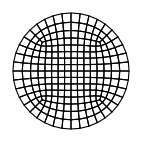

```mathematica
disk["Wireframe"]
```

```mathematica
mesh = ExtrudeMesh[disk,h,3]
```

ElementMesh[{{-1.,1.},{-1.,1.},{0.,0.6}},{HexahedronElement[<660>]}]

```mathematica
mesh["Wireframe"]
```

-Graphics3D-

```mathematica
coords=mesh[[1]]//Chop[#,10^-7]&;
elements=mesh[[2,1,1]];
```

```mathematica
numVertices=Length[coords];
numElements=Length[elements]
```

660

```mathematica
(*Optional:boundary data*)
boundaryElements=mesh["BoundaryElements"][[1,1]];
numBoundary=Length[boundaryElements]
```

560

```mathematica
(* Assign boundary attributes *)
```

```mathematica
boundaryElements1 := Module[{elcoords,belements1,zcoords,count},
belements1 = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,3]]<= 0.0001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==4, AppendTo[belements1,i]
 ];
,{i,boundaryElements}];
belements1
]
```

```mathematica
boundaryElements2 := Module[{elcoords,belements2,zcoords,count},
belements2 = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,3]]>= (h-0.0001) , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==4, AppendTo[belements2,i]
 ];
,{i,boundaryElements}];
belements2
]
```

```mathematica
boundaryElements3 := Module[{elcoords,belements3,zcoords,count},
belements3 = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,3]]>= (h-0.0001) || elcoords[[n,3]]<= 0.0001, count+=1
];
,{n,1,Length[elcoords]}
];
If[
count!=4, AppendTo[belements3,i]
 ];
,{i,boundaryElements}];
belements3
]
```

```mathematica
{boundaryElements1//Length,boundaryElements2//Length,boundaryElements3//Length}
```

{220,220,120}

```mathematica
boundaryElements//Length
```

560

MFEM Geometry types:
# POINT       		= 0
# SEGMENT     		= 1
# TRIANGLE    		= 2
# SQUARE      		= 3
# TETRAHEDRON 	= 4
# CUBE        		= 5

```mathematica
(*Build vertex section*)
vertexSection=StringJoin["vertices\n",ToString[numVertices],"\n",ToString[3],"\n",StringJoin[Table[StringJoin[ToString[NumberForm[x[[1]],7]]," ",ToString[NumberForm[x[[2]],7]]," ",ToString[NumberForm[x[[3]],7]],"\n"],{x,coords}]]];
```

```mathematica
(*Build elements section*)
elementSection=StringJoin["elements\n",ToString[numElements],"\n",StringJoin[Table[StringJoin["1 5 ",(*1=region attr,5=cube, *)StringRiffle[ToString/@(elem-1)," "],"\n"],{elem,elements}]]];
```

```mathematica
(*Boundary section*)
boundarySection1=StringJoin["boundary\n",ToString[numBoundary],"\n",StringJoin[Table[StringJoin["1 3 ",(*1=boundary attr,3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements1}]]];
```

```mathematica
boundarySection2=StringJoin[
StringJoin[Table[StringJoin["2 3 ",(*2=boundary attr,3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements2}]]];
```

```mathematica
boundarySection3=StringJoin[
StringJoin[Table[StringJoin["3 3 ",(*3=boundary attr,3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements3}]]];
```

```mathematica
mfemMeshContent=StringJoin["MFEM mesh v1.0\n\n","dimension\n"<>"3"<>"\n\n",elementSection,"\n",boundarySection1,boundarySection2,boundarySection3,"\n",vertexSection];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Aashutosh/Academic/Software/MFEM_new/projects/ViscoelasticityPDMS/mesh

```mathematica
Export["PDMSpuck-scaled-hex.mesh",mfemMeshContent,"Text"]
```

PDMSpuck-scaled-hex.mesh

### Tet Mesh

```mathematica
a = 1; h = 0.6;
```

```mathematica
disk = DiskMesh[{0,0},a,10]
```

ElementMesh[{{-1.,1.},{-1.,1.}},{QuadElement[<220>]}]

```mathematica
disk["Wireframe"]
```

-Graphics-

```mathematica
diskmesh = ExtrudeMesh[disk,h,3]
```

ElementMesh[{{-1.,1.},{-1.,1.},{0.,0.5}},{HexahedronElement[<660>]}]

```mathematica
mesh = HexToTetrahedronMesh[diskmesh]
mesh["Wireframe"]
```

ElementMesh[{{-1.,1.},{-1.,1.},{0.,0.5}},{TetrahedronElement[<3960>]}]

-Graphics3D-

```mathematica
coords=mesh[[1]]//Chop[#,10^-7]&;
elements=mesh[[2,1,1]];
```

```mathematica
numVertices=Length[coords];
numElements=Length[elements]
```

3960

```mathematica
(*Optional:boundary data*)
boundaryElements=mesh["BoundaryElements"][[1,1]];
numBoundary=Length[boundaryElements]
```

1360

```mathematica
(* Assign boundary attributes *)
```

```mathematica
boundaryElements1 := Module[{elcoords,belements1,zcoords,count},
belements1 = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,3]]<= 0.0001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==3, AppendTo[belements1,i]
 ];
,{i,boundaryElements}];
belements1
]
```

```mathematica
boundaryElements2 := Module[{elcoords,belements2,zcoords,count},
belements2 = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,3]]>= (h-0.0001) , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==3, AppendTo[belements2,i]
 ];
,{i,boundaryElements}];
belements2
]
```

```mathematica
boundaryElements3 := Module[{elcoords,belements3,zcoords,count},
belements3 = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,3]]>= (h-0.0001) || elcoords[[n,3]]<= 0.0001, count+=1
];
,{n,1,Length[elcoords]}
];
If[
count!=3, AppendTo[belements3,i]
 ];
,{i,boundaryElements}];
belements3
]
```

```mathematica
bel={boundaryElements1//Length,boundaryElements2//Length,boundaryElements3//Length}
bel//Total
```

{440,440,480}

1360

```mathematica
boundaryElements//Length
```

1360

MFEM Geometry types:
# POINT       		= 0
# SEGMENT     		= 1
# TRIANGLE    		= 2
# SQUARE      		= 3
# TETRAHEDRON 	= 4
# CUBE        		= 5

```mathematica
(*Build vertex section*)
vertexSection=StringJoin["vertices\n",ToString[numVertices],"\n",ToString[3],"\n",StringJoin[Table[StringJoin[ToString[NumberForm[x[[1]],7]]," ",ToString[NumberForm[x[[2]],7]]," ",ToString[NumberForm[x[[3]],7]],"\n"],{x,coords}]]];
```

```mathematica
(*Build elements section*)
elementSection=StringJoin["elements\n",ToString[numElements],"\n",StringJoin[Table[StringJoin["1 4 ",(*1=region attr,4=tetrahedron, *)StringRiffle[ToString/@(elem-1)," "],"\n"],{elem,elements}]]];
```

```mathematica
(*Boundary section*)
boundarySection1=StringJoin["boundary\n",ToString[numBoundary],"\n",StringJoin[Table[StringJoin["1 2 ",(*1=boundary attr,2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements1}]]];
```

```mathematica
boundarySection2=StringJoin[
StringJoin[Table[StringJoin["2 2 ",(*2=boundary attr,2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements2}]]];
```

```mathematica
boundarySection3=StringJoin[
StringJoin[Table[StringJoin["3 2 ",(*3=boundary attr,2=triangle*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements3}]]];
```

```mathematica
mfemMeshContent=StringJoin["MFEM mesh v1.0\n\n","dimension\n"<>"3"<>"\n\n",elementSection,"\n",boundarySection1,boundarySection2,boundarySection3,"\n",vertexSection];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Aashutosh/Academic/Software/MFEM/Projects/ViscoelasticityPDMS/mesh

```mathematica
Export["PDMSpuck-scaled-tet.mesh",mfemMeshContent,"Text"]
```

PDMSpuck-scaled-tet.mesh

### Hex Mesh (unscaled)

```mathematica
h = 0.002;r =1.5*h
```

0.003

ElementMesh[{{-0.003,0.003},{-0.003,0.003}},{QuadElement[<220>]}]

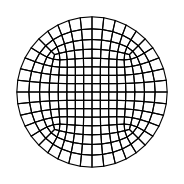

```mathematica
disk = DiskMesh[{0,0},r,10]
disk["Wireframe"]
```

```mathematica
mesh = ExtrudeMesh[disk,h,5]
```

ElementMesh[{{-0.003,0.003},{-0.003,0.003},{0.,0.002}},{HexahedronElement[<1100>]}]

```mathematica
mesh["Wireframe"]
```

-Graphics3D-

```mathematica
coords=mesh[[1]]//Chop[#,10^-7]&;
elements=mesh[[2,1,1]];
```

```mathematica
numVertices=Length[coords];
numElements=Length[elements]
```

1100

```mathematica
(*Optional:boundary data*)
boundaryElements=mesh["BoundaryElements"][[1,1]];
numBoundary=Length[boundaryElements]
```

640

```mathematica
(* Assign boundary attributes *)
```

```mathematica
boundaryElements1 := Module[{elcoords,belements1,zcoords,count},
belements1 = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,3]]<= 0.0001 , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==4, AppendTo[belements1,i]
 ];
,{i,boundaryElements}];
belements1
]
```

```mathematica
boundaryElements2 := Module[{elcoords,belements2,zcoords,count},
belements2 = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,3]]>= (h-0.0001) , count+=1
];
,{n,1,Length[elcoords]}
];
If[
count==4, AppendTo[belements2,i]
 ];
,{i,boundaryElements}];
belements2
]
```

```mathematica
boundaryElements3 := Module[{elcoords,belements3,zcoords,count},
belements3 = {};
Do[
count = 0;
elcoords = coords[[i]];
Do[
If[
elcoords[[n,3]]>= (h-0.0001) || elcoords[[n,3]]<= 0.0001, count+=1
];
,{n,1,Length[elcoords]}
];
If[
count!=4, AppendTo[belements3,i]
 ];
,{i,boundaryElements}];
belements3
]
```

```mathematica
{boundaryElements1//Length,boundaryElements2//Length,boundaryElements3//Length}//Total
```

640

```mathematica
boundaryElements//Length
```

640

MFEM Geometry types:
# POINT       		= 0
# SEGMENT     		= 1
# TRIANGLE    		= 2
# SQUARE      		= 3
# TETRAHEDRON 	= 4
# CUBE        		= 5

```mathematica
(*Build vertex section*)
vertexSection=StringJoin["vertices\n",ToString[numVertices],"\n",ToString[3],"\n",StringJoin[Table[StringJoin[ToString[NumberForm[x[[1]],7]]," ",ToString[NumberForm[x[[2]],7]]," ",ToString[NumberForm[x[[3]],7]],"\n"],{x,coords}]]];
```

```mathematica
(*Build elements section*)
elementSection=StringJoin["elements\n",ToString[numElements],"\n",StringJoin[Table[StringJoin["1 5 ",(*1=region attr,5=cube, *)StringRiffle[ToString/@(elem-1)," "],"\n"],{elem,elements}]]];
```

```mathematica
(*Boundary section*)
boundarySection1=StringJoin["boundary\n",ToString[numBoundary],"\n",StringJoin[Table[StringJoin["1 3 ",(*1=boundary attr,3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements1}]]];
```

```mathematica
boundarySection2=StringJoin[
StringJoin[Table[StringJoin["2 3 ",(*2=boundary attr,3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements2}]]];
```

```mathematica
boundarySection3=StringJoin[
StringJoin[Table[StringJoin["3 3 ",(*3=boundary attr,3=square*)StringRiffle[ToString/@(b-1)," "],"\n"],{b,boundaryElements3}]]];
```

```mathematica
mfemMeshContent=StringJoin["MFEM mesh v1.0\n\n","dimension\n"<>"3"<>"\n\n",elementSection,"\n",boundarySection1,boundarySection2,boundarySection3,"\n",vertexSection];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Aashutosh/Academic/Software/MFEM_new/projects/ViscoelasticityPDMS/mesh

```mathematica
Export["PDMSpuck-unscaled-hex.mesh",mfemMeshContent,"Text"]
```

PDMSpuck-unscaled-hex.mesh